```mathematica
Module[{a=158.4,b=0.288,c,d,e},NonlinearModelFit[data,Re[{c/(1+Exp[d-Log[a/(b* x)-1/b]/e])}],{{d,2.6},{c,160},{e,0.45}},x]]
```

FittedModel[157.671 Re[1/(1+(2.51409×10^-11)/(-«19»+«1»)^(«19»))]]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.86541 | 0.00671328 | 724.745 | 9.49225×10^-14
x | 0.674422 | 0.12464 | 5.41096 | 0.0029163

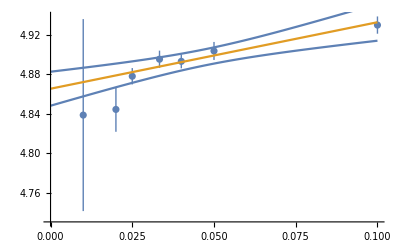

```mathematica
data={{{1/10,4.92997},ErrorBar[0.00875039]},{{1/20,4.90374},ErrorBar[0.00912412]},{{1/25,4.89318},ErrorBar[0.00707122]},{{1/30,4.89534},ErrorBar[0.00870608]},{{1/40,4.87807},ErrorBar[0.00829155]},{{1/50,4.84442},ErrorBar[0.0226886]},{{1/100,4.83867},ErrorBar[0.0973819]}};
error=data[[All,2]]/.ErrorBar[x_]->x;
t=Table[{data[[i,1,1]],Around[data[[i,1,2]],error[[i]]]},{i,Length[error]}];
lmf=LinearModelFit[data[[All,1]],x,x,Weights->1/error^2];
lmf["ParameterTable"]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,0.1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/yinsh/Chi8/data/freezeout/fitSTAR

```mathematica
data=Import["stardata.dat"][[All,{2,4,5}]]
```

{{399.8,143.8,2.7},{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5},{69.2,164.3,3.6},{27.,167.8,4.2}}

{2.7,3.2,3.1,3.,3.5,3.6,4.2}

| Estimate | Standard Error | t-Statistic | P-Value
c | 162.217 | 1.55268 | 104.476 | 1.52334×10^-9
e | 0.453047 | 0.0164501 | 27.5407 | 1.18117×10^-6

162.217/(1+13.4637/(-3.47222+4539.93/x)^2.20728)

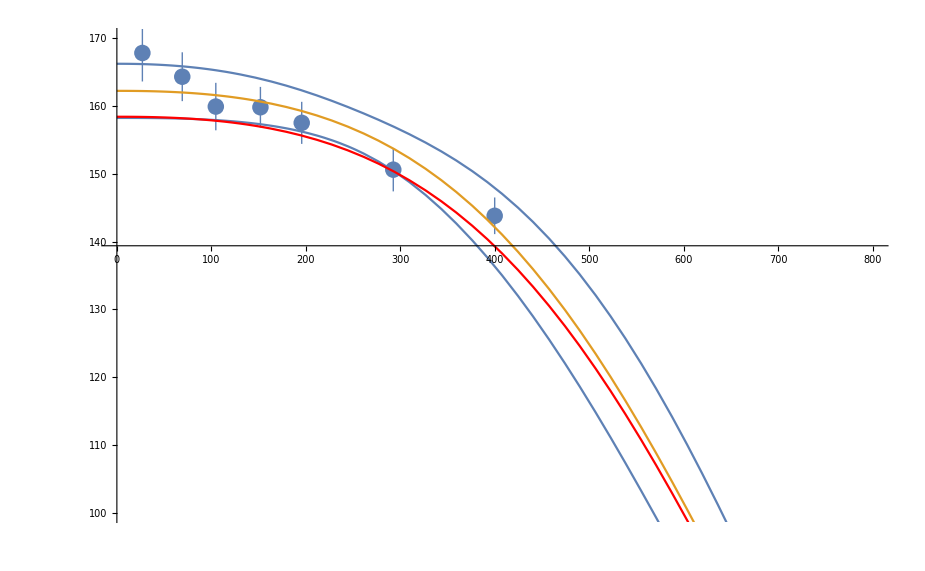

```mathematica
(*data={{{1/10,4.92997},ErrorBar[0.00875039]},{{1/20,4.90374},ErrorBar[0.00912412]},{{1/25,4.89318},ErrorBar[0.00707122]},{{1/30,4.89534},ErrorBar[0.00870608]},{{1/40,4.87807},ErrorBar[0.00829155]},{{1/50,4.84442},ErrorBar[0.0226886]},{{1/100,4.83867},ErrorBar[0.0973819]}};*)
error=data[[All,-1]]
t=Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}];
lmf=NonlinearModelFit[data[[All,{1,2}]],c/(1+Exp[2.6-Log[1307.5/(0.288* x)-1/0.288]/e]),{{c,160},{e,1/2}},x,Weights->1/error^2];
lmf["ParameterTable"]
lmf[x]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red],PlotRange->{{0,800},{100,170}}]
```

```mathematica
lmf["MeanPredictionBands"]
```

```mathematica
export={lmf["MeanPredictionBands"],lmf[x]}/.x->{22.3123,68.9203,78.4475,106.892,148.986,196.77,252.608,303.224,406.359}
```

{{{158.221,158.125,158.083,157.888,157.349,156.174,153.543,149.421,135.24},{166.177,165.833,165.708,165.208,164.087,162.237,159.38,156.256,147.186}},{162.199,161.979,161.895,161.548,160.718,159.206,156.461,152.838,141.213}}

```mathematica
exp7=Transpose[{{158.22131413171184,158.12543008868985,158.08272958026592,157.88823578063685,157.3488875625452,156.1743113574977,153.54260856723175,149.42096014040877,135.23995860136924},{166.17661492225972,165.8333694752669,165.7082060234118,165.20772158533637,164.0873523363664,162.2373987283354,159.37997420465115,156.25580406364318,147.18556703491257},{162.19896452698578,161.97939978197837,161.89546780183886,161.5479786829866,160.7181199494558,159.20585504291654,156.46129138594145,152.83838210202597,141.2127628181409}}]
```

{{158.221,166.177,162.199},{158.125,165.833,161.979},{158.083,165.708,161.895},{157.888,165.208,161.548},{157.349,164.087,160.718},{156.174,162.237,159.206},{153.543,159.38,156.461},{149.421,156.256,152.838},{135.24,147.186,141.213}}

```mathematica
Export["sevenpointfit.dat",exp7]
```

sevenpointfit.dat

```mathematica
Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}]
```

{{399.8,143.82.7},{292.5,150.63.2},{195.6,157.53.1},{151.9,159.83.0},{104.7,159.93.5},{69.2,164.4.},{27.,168.4.}}

```mathematica
error=data[[All,-1]]
```

{2.7,3.2,3.1,3.,3.5,3.6,4.2}

```mathematica
{lmf["MeanPredictionBands"],lmf[x]}/.x->100
```

{{157.946,165.347},161.646}

{{399.8,143.8,2.7},{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5},{69.2,164.3,3.6},{27.,167.8,4.2}}

```mathematica
data={{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5}}
```

{{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5}}

{3.2,3.1,3.,3.5}

| Estimate | Standard Error | t-Statistic | P-Value
c | 161.439 | 0.507481 | 318.119 | 9.88131×10^-6
e | 0.474767 | 0.00776693 | 61.1267 | 0.000267525

161.439/(1+13.4637/(-3.47222+4539.93/x)^2.1063)

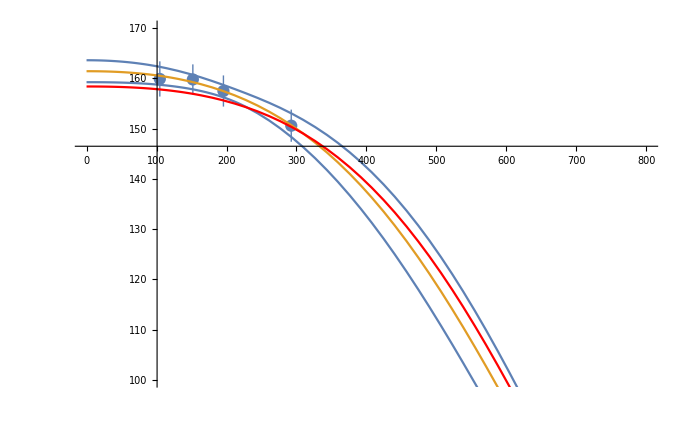

```mathematica
error=data[[All,-1]]
t=Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}];
lmf=NonlinearModelFit[data[[All,{1,2}]],c/(1+Exp[2.6-Log[1307.5/(0.288* x)-1/0.288]/e]),{{c,160},{e,1/2}},x,Weights->1/error^2];
lmf["ParameterTable"]
lmf[x]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red],PlotRange->{{0,800},{100,170}}]
```

```mathematica
export={lmf["MeanPredictionBands"],lmf[x]}/.x->{22.3123,68.9203,78.4475,106.892,148.986,196.77,252.608,303.224,406.359}
```

{{{159.245,159.077,159.008,158.705,157.908,156.189,152.382,147.111,131.499},{163.572,163.084,162.913,162.249,160.824,158.648,155.652,152.259,141.482}},{161.408,161.08,160.961,160.477,159.366,157.418,154.017,149.685,136.49}}

```mathematica
exp4=Transpose[{{159.2451405725481,159.07695501798005,159.00758761997403,158.7051389360926,157.9077370306953,156.18867704217698,152.38220395585265,147.11058393969924,131.4986919237775},{163.571758650295,163.08394426432952,162.91348743423922,162.24896859974936,160.82423168700186,158.64794794776444,155.65171560134903,152.25943571025854,141.48195097574987},{161.40844961142156,161.0804496411548,160.96053752710662,160.47705376792098,159.36598435884858,157.4183124949707,154.01695977860084,149.6850098249789,136.49032144976368}}]
```

{{159.245,163.572,161.408},{159.077,163.084,161.08},{159.008,162.913,160.961},{158.705,162.249,160.477},{157.908,160.824,159.366},{156.189,158.648,157.418},{152.382,155.652,154.017},{147.111,152.259,149.685},{131.499,141.482,136.49}}

```mathematica
Export["fourpointfit.dat",exp4]
```

fourpointfit.dat